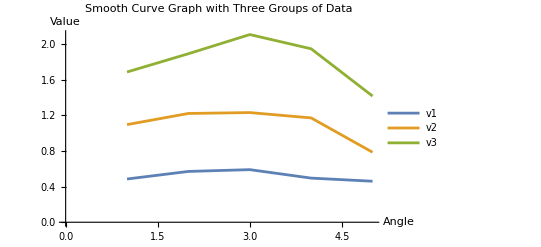

```mathematica
data={{25,0.485},{35,0.570},{45,0.590},{55,0.495},{65,0.460}};
newData={{25,1.095},{35,1.220},{45,1.230},{55,1.170},{65,0.785}};
latestData={{25,1.685},{35,1.890},{45,2.105},{55,1.945},{65,1.415}};

v1=data[[All,2]];
v2=newData[[All,2]];
v3=latestData[[All,2]];

ListLinePlot[{v1,v2,v3},PlotLegends->{"v1","v2","v3"},AxesLabel->{"Angle","Value"},PlotLabel->"Smooth Curve Graph with Three Groups of Data"]
```

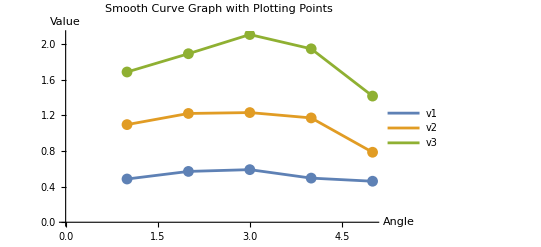

```mathematica
data={{25,0.485},{35,0.570},{45,0.590},{55,0.495},{65,0.460}};
newData={{25,1.095},{35,1.220},{45,1.230},{55,1.170},{65,0.785}};
latestData={{25,1.685},{35,1.890},{45,2.105},{55,1.945},{65,1.415}};

v1=data[[All,2]];
v2=newData[[All,2]];
v3=latestData[[All,2]];

ListLinePlot[{v1,v2,v3},PlotLegends->{"v1","v2","v3"},AxesLabel->{"Angle","Value"},Mesh->All,PlotLabel->"Smooth Curve Graph with Plotting Points"]
```

```mathematica
data={{25,0.485},{35,0.570},{45,0.590},{55,0.495},{65,0.460}};
newData={{25,1.095},{35,1.220},{45,1.230},{55,1.170},{65,0.785}};
latestData={{25,1.685},{35,1.890},{45,2.105},{55,1.945},{65,1.415}};

(*Extracting the second element (v1,v2,v3) from each list*)
v1=data[[All,2]];
v2=newData[[All,2]];
v3=latestData[[All,2]];

(*Creating a smooth curve graph*)
ListLinePlot[{v1,v2,v3},DataRange->{25,65},PlotLegends->{"v1","v2","v3"},Frame->True,FrameLabel->{"Angle","Value"},PlotLabel->"Smooth Curve Graph of Three Groups of Data"]
```

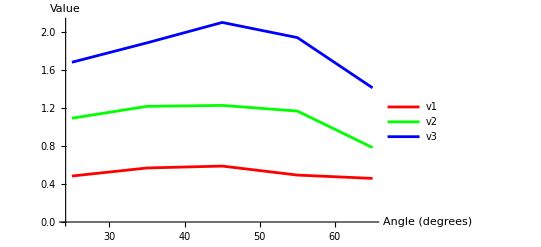

```mathematica
data={{25,0.485},{35,0.570},{45,0.590},{55,0.495},{65,0.460}};
newData={{25,1.095},{35,1.220},{45,1.230},{55,1.170},{65,0.785}};
latestData={{25,1.685},{35,1.890},{45,2.105},{55,1.945},{65,1.415}};

v1=data[[All,2]];
v2=newData[[All,2]];
v3=latestData[[All,2]];

ListLinePlot[{v1,v2,v3},DataRange->{25,65},PlotLegends->{"v1","v2","v3"},AxesLabel->{"Angle (degrees)","Value"},PlotStyle->{Red,Green,Blue}]
```

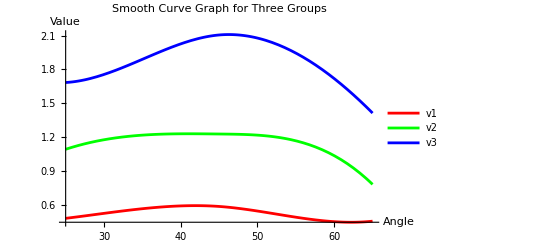

```mathematica
data={{25,0.485},{35,0.570},{45,0.590},{55,0.495},{65,0.460}};
newData={{25,1.095},{35,1.220},{45,1.230},{55,1.170},{65,0.785}};
latestData={{25,1.685},{35,1.890},{45,2.105},{55,1.945},{65,1.415}};

v1=data[[All,2]];
v2=newData[[All,2]];
v3=latestData[[All,2]];

(*Smooth interpolation function for each group*)
f1=Interpolation[Transpose[{data[[All,1]],v1}],Method->"Spline"];
f2=Interpolation[Transpose[{newData[[All,1]],v2}],Method->"Spline"];
f3=Interpolation[Transpose[{latestData[[All,1]],v3}],Method->"Spline"];

(*Plotting the smooth curves*)
Plot[{f1[x],f2[x],f3[x]},{x,25,65},PlotLegends->{"v1","v2","v3"},AxesLabel->{"Angle","Value"},PlotLabel->"Smooth Curve Graph for Three Groups",PlotStyle->{Red,Green,Blue}]
```

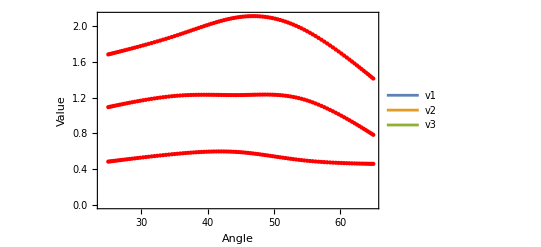

```mathematica
data={{25,0.485},{35,0.570},{45,0.590},{55,0.495},{65,0.460}};
newData={{25,1.095},{35,1.220},{45,1.230},{55,1.170},{65,0.785}};
latestData={{25,1.685},{35,1.890},{45,2.105},{55,1.945},{65,1.415}};

v1=data[[All,2]];
v2=newData[[All,2]];
v3=latestData[[All,2]];

ListLinePlot[{v1,v2,v3},DataRange->{25,65},PlotLegends->{"v1","v2","v3"},FrameLabel->{"Angle","Value"},Frame->True,Mesh->All,MeshStyle->Directive[PointSize[Medium],Red],InterpolationOrder->3]
```

```mathematica
data={{25,0.485},{35,0.570},{45,0.590},{55,0.495},{65,0.460}};
newData={{25,1.095},{35,1.220},{45,1.230},{55,1.170},{65,0.785}};
latestData={{25,1.685},{35,1.890},{45,2.105},{55,1.945},{65,1.415}};

(*Extracting the second element (v1,v2,v3) from each list*)
v1=data[[All,2]];
v2=newData[[All,2]];
v3=latestData[[All,2]];

(*Forming a smooth curve graph and showing the plot*)
ListLinePlot[{v1,v2,v3},PlotLegends->{"v1","v2","v3"},AxesLabel->{"Angle","Values"},PlotLabel->"Smooth Curve Graph with Three Groups of Data"]
```

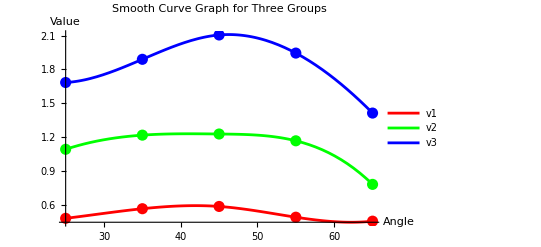

```mathematica
data={{25,0.485},{35,0.570},{45,0.590},{55,0.495},{65,0.460}};
newData={{25,1.095},{35,1.220},{45,1.230},{55,1.170},{65,0.785}};
latestData={{25,1.685},{35,1.890},{45,2.105},{55,1.945},{65,1.415}};

v1=data[[All,2]];
v2=newData[[All,2]];
v3=latestData[[All,2]];

(*Smooth interpolation function for each group*)
f1=Interpolation[Transpose[{data[[All,1]],v1}],Method->"Spline"];
f2=Interpolation[Transpose[{newData[[All,1]],v2}],Method->"Spline"];
f3=Interpolation[Transpose[{latestData[[All,1]],v3}],Method->"Spline"];

(*Plotting the smooth curves with data points*)
Plot[{f1[x],f2[x],f3[x]},{x,25,65},PlotLegends->{"v1","v2","v3"},AxesLabel->{"Angle","Value"},PlotLabel->"Smooth Curve Graph for Three Groups",PlotStyle->{Red,Green,Blue},Epilog->{Red,PointSize[0.02],Point[data],Green,PointSize[0.02],Point[newData],Blue,PointSize[0.02],Point[latestData]}]
```